```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@AbsoluteOptions[g,PlotRange],Sequence@@Options[g,Epilog]]
SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->1}];
t0=10.^-8;
t1=10^2;
Nt=101;
times=Table[t0*(t1/t0)^(i/(Nt-1)),{i,0,(Nt-1)}];
tind0=0;
tind1=(Log[10^-5]-Log[t0])/(Log[t1]-Log[t0])*Nt;
tind2=(Log[10^-3]-Log[t0])/(Log[t1]-Log[t0])*Nt;
tind3=(Log[10^2]-Log[t0])/(Log[t1]-Log[t0])*Nt;
c1=Lighter[Orange];
c2=Lighter[Red];
c3=Lighter[Blue];
c4=Lighter[Green];
cf[tind_]:=Piecewise[{{Blend[{c1,c2},(tind-tind0)/(tind1-tind0)],tind<=tind1},{Blend[{c2,c3},(tind-tind1)/(tind2-tind1)],tind≤tind2},{Blend[{c3,c4},(tind-tind2)/(tind3-tind2)],tind>tind2}}];
cb1=ListDensityPlot[Flatten[Table[{i,j,i},{i,1,Length[times]},{j,1,2}],1],ColorFunctionScaling->False,ColorFunction->cf,AspectRatio->1/12,PlotRange->{{1,101},{1,2}},PlotRangePadding->None,FrameTicks->{{None,None},{None,Table[{i,Superscript[10,3+Round[Log[times[[i]]]/Log[10]]]},{i,1,Length[times],20}]}},FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->200,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{None,DisplayForm[RowBox[{t," (ms)"}]]}}];
cb2=ListDensityPlot[Flatten[Table[{j,i,i},{i,1,Length[times]},{j,1,2}],1],ColorFunctionScaling->False,ColorFunction->cf,AspectRatio->12,PlotRange->{{1,2},{0,101}},PlotRangePadding->None,FrameTicks->{{None,Table[{i,Superscript[10,3+Round[Log[times[[i]]]/Log[10]]]},{i,1,Length[times],20}]},{None,None}},FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->{Automatic,200},LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{None,DisplayForm[RowBox[{t," (ms)"}]]}}];
```

/Users/zack/Documents/ignition/cantera/ratematrix

#### fig1

{63835,9,1827.95}

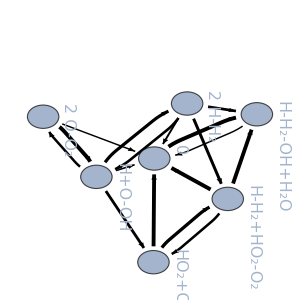

```mathematica
filebase="data/nodimred/10";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
ind=First@FirstPosition[multiindices,dat[[2]]];
indices=Join[{ind},First/@Position[Normal[A[[ind]]],u_/;u>0]];
spforms={Subscript["H", 2],"H","O",Subscript["O", 2],"OH","H_2O",Subscript["HO", 2],Subscript["H_2O", 2],0};
vertexlabels=Total[spforms*(#-dat[[2]])]&/@multiindices[[indices]];
mat=Normal[A[[indices,indices]]]-DiagonalMatrix[Diagonal[Normal[A[[indices,indices]]]]]/.(u_/;u<1->0);p1=Rotate[GraphPlot[mat,VertexLabels->Table[i->Rotate[Style[vertexlabels[[i]],16],-Pi/2],{i,1,Length[indices]}],ImageSize->300,DataRange->{{-1,1},{-1,1}},VertexSize->0.5,DirectedEdges->True,EdgeShapeFunction->({Black, Opacity[1],AbsoluteThickness[0.2*Log[#2/.(DirectedEdge[a1_,a2_]:>mat[[a1,a2]])]],Arrowheads[0.003*Log[#2/.(DirectedEdge[a1_,a2_]:>mat[[a1,a2]])]],Arrow[#1, 0.2]} & )],Pi/2]
```

```mathematica
filebase="data/dimred3/10"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];

A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
scale=40000;
dim2=10000;
p0=
Legended[rasterizeBackground[MatrixPlot[Abs[A]/scale,ImageSize->350,MaxPlotPoints->200,ColorFunctionScaling->False,ColorFunction->(If[#==0,White,Blend[{Lighter[Blue],Lighter[Red]},#]]&),FrameTicks->{Table[Round[i],{i,1,dim2,(dim2-1)/4}],Table[Round[i],{i,1,dim2,(dim2-1)/4}]},FrameLabel->{{i,None},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],MatrixPlot[Table[i,{i,0,100},{j,0,100}],AspectRatio->10,ImageSize->{Automatic,200},FrameStyle->Directive[Black,AbsoluteThickness[2]],ColorFunction->(If[#==0,White,Blend[{Lighter[Blue],Lighter[Red]},#/100]]&),ColorFunctionScaling->False,FrameLabel->{{None,DisplayForm[RowBox[{Abs[Subscript[W,ij]],"/",HoldForm[10^4]}]]},{None,None}},FrameTicks->{{None,{{1,0},{26,1},{51,2},{76,3},{101,4}}},{None,None}},DataReversed->True,LabelStyle->Directive[16,Black]]];
p0
```

data/dimred3/10

{11106,9,0}

-Graphics-

```mathematica
filebase="data/combustionoh";
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
concentrations=Transpose[Partition[BinaryReadList[filebase<>"concentrations.npy","Real64"][[17;;-1]],9]];
rates=Transpose[Partition[BinaryReadList[filebase<>"rates.npy","Real64"][[17;;-1]],28]];
rstois=Transpose[Partition[BinaryReadList[filebase<>"rstois.npy","Integer64"][[17;;-1]],28]];
pstois=Transpose[Partition[BinaryReadList[filebase<>"pstois.npy","Integer64"][[17;;-1]],28]];
species={"H2","H","O","O2","OH","H2O","HO2","H2O2","AR"};
sptime[text_]:=First@FirstPosition[Accumulate[10^-12+concentrations[[First@FirstPosition[species,text]]]]/Total[10^-12+concentrations[[First@FirstPosition[species,text]]]],u_/;u>0.5]/Nt
sptimemin=Min[sptime/@species];
sptimemax=Max[sptime/@species];
spcol[text_]:=Blend[{Cyan,Orange},(sptime[text]-sptimemin)/(sptimemax-sptimemin)]
nreactions=Length[rstois];
Nt=Length[concentrations[[1]]];
tint=Interpolation[Transpose[{Range[Nt]/Nt,times}]];
reactants=Table[Extract[species,Position[rstois[[i]],u_/;u>0]],{i,1,nreactions}];
products=Table[Extract[species,Position[pstois[[i]],u_/;u>0]],{i,1,nreactions}];
r1=1.5;
r2=1;
colors={Lighter[Blue],Lighter[Red]};
weights=Mean/@rates;
weights2=First@FirstPosition[Abs[#],Max[Abs[#]]]&/@rates/Nt;
wscale=Max[Abs[weights]];
ethrs=10^-64;
ethick=0.003;
shown=Flatten[Position[weights,u_/;Abs[u]>ethrs]];
edges=Table[If[weights[[i]]>0,Join[Table[reactants[[i,j]]->i,{j,1,Length[reactants[[i]]]}],Table[i->products[[i,j]],{j,1,Length[products[[i]]]}]],Join[Table[i->reactants[[i,j]],{j,1,Length[reactants[[i]]]}],Table[products[[i,j]]->i,{j,1,Length[products[[i]]]}]]],{i,1,nreactions}];
vertices=Union[species,DeleteDuplicates[Flatten[edges][[All,1]],Flatten[edges][[All,2]]]];
center=DeleteDuplicates[Join[Flatten[edges[[shown,All,1]]],Flatten[edges[[shown,All,2]]]]];
centerspecies=SortBy[Complement[DeleteDuplicates[DeleteDuplicates[Join[Flatten[edges[[shown,All,1]]],Flatten[edges[[shown,All,2]]]]]],Range[nreactions]],spcol[#]&];
centerreactions=Complement[center,centerspecies];
bottomspecies=SortBy[Complement[species,centerspecies],spcol[#]&];
bottomreactions=Complement[Range[nreactions],centerreactions];
rvcs=GraphEmbedding[PathGraph[Flatten[Position[weights,u_/;Abs[u]>ethrs]],GraphLayout->"SpiralEmbedding"]];
rvcs2=GraphEmbedding[PathGraph[Flatten[Position[weights,u_/;Abs[u]<=ethrs]],GraphLayout->"SpiralEmbedding"]];
{xmax,xmin,ymax,ymin}={Max[rvcs[[All,1]]],Min[rvcs[[All,1]]],Max[rvcs[[All,2]]],Min[rvcs[[All,2]]]};
{xmax2,xmin2,ymax2,ymin2}={Max[rvcs2[[All,1]]],Min[rvcs2[[All,1]]],Max[rvcs2[[All,2]]],Min[rvcs2[[All,2]]]};
trange=Quantile[Extract[weights2,Position[weights,u_/;Abs[u]>ethrs]],{0.25,0.75}];
eweight[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights[[edge[[1]]]],weights[[edge[[2]]]]];
ecolor[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights2[[edge[[1]]]],weights2[[edge[[2]]]]];
vsize[text_]:=0.005+0.08*(Log[Max[Mean[concentrations[[First@FirstPosition[species,text]]]],10^-8]]/Log[10]+8)/8;
sizes={1.0,0.1,0.01,0.001,0.0001};
wsizes=Table[z/.First@Solve[(Log[Abs[z/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])==i*1.0/5,z],{i,5,1,-1}];

weights2=First@FirstPosition[Abs[#],Max[Abs[#]]]&/@rates;
ecolor[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights2[[edge[[1]]]],weights2[[edge[[2]]]]]
plot=Graph[Flatten[{SortBy[species,sptime],SortBy[Range[Length[edges]],ecolor[edges[[#,1]]]&]}],Flatten[edges],GraphLayout->"BipartiteEmbedding",VertexLabels->(#->If[IntegerQ[#],"",Style[#,16]]&/@vertices),VertexStyle->(#->If[ValueQ[Element[#,Integers]],{If[MemberQ[bottomreactions,#],{Opacity[0],EdgeForm[None]},{Opacity[1],EdgeForm[Black]}],Black},If[MemberQ[centerspecies,#],{Hue[0.6,0.2,0.8],EdgeForm[Black]},{Opacity[1.0],Hue[0.6,0.2,0.8],EdgeForm[Black]}]]&/@vertices),
VertexSize->(#->If[ValueQ[Element[#,Integers]],{"Scaled",0.005},If[MemberQ[centerspecies,#],{"Scaled",0.05},{"Scaled",0.05}]]&/@vertices),EdgeStyle->(#-> If[Abs[eweight[#]]≤0,{Directive[Opacity[0]]},{Directive[Opacity[1.0]],Directive[cf[ecolor[#]]],Thickness[ethick],Arrowheads[{{Abs[10*ethick],1.0}}]}]&/@Flatten[edges]),EdgeShapeFunction->((If[#[[1,1]]>#[[2,1]],{Arrow[#,{0.0,0.075}]},{Arrow[#,{0.0,0.015}]}])&),ImageSize->{300,Automatic}];
p2=Grid[{{cb1},{plot}}];
```

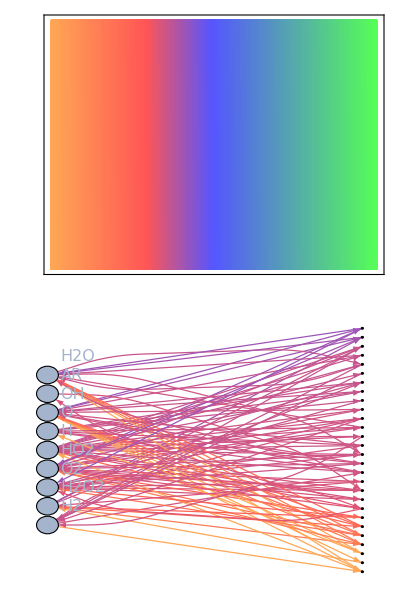
-Graphics- | -Graphics- | -Graphics-

```mathematica
p=Grid[{{p2,p1,p0}}]
```

#### fig2

{data/dimred3/3,data/dimred3/4,data/dimred3/5,data/dimred3/6,data/dimred3/7,data/dimred3/8,data/dimred3/9,data/dimred3/10,data/dimred3/11,data/dimred3/12,data/dimred3/13,data/dimred3/14,data/dimred3/15}

{data/nodimred/3,data/nodimred/4,data/nodimred/5,data/nodimred/6,data/nodimred/7,data/nodimred/8,data/nodimred/9,data/nodimred/10}

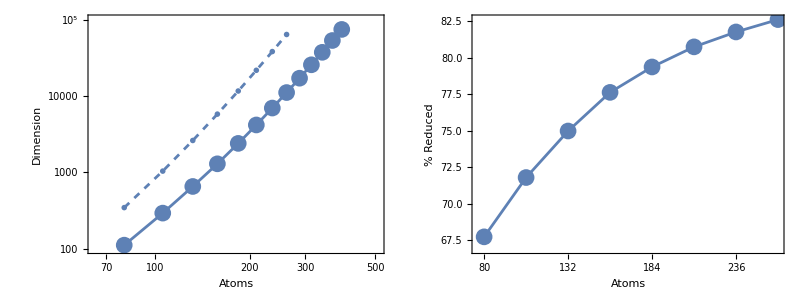

fig2.pdf

```mathematica
initials={};
filebases=Table["data/dimred3/"<>ToString[i],{i,3,15,1}]
dims={};
Do[
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];AppendTo[dims,dim];,{filebase,filebases}]
filebases=Table["data/nodimred/"<>ToString[i],{i,3,10,1}]
dims2={};
Do[
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];AppendTo[dims2,dim];,{filebase,filebases}]
p=Grid[{{Show[ListLogLogPlot[Transpose[{2+(20+2+4)*(Range[Length[dims]]+2),dims}],AspectRatio->1,Joined->True,Axes->False,Frame->True,FrameLabel->{"Atoms","Dimension"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[AbsoluteThickness[2]],ImageSize->300,ImagePadding->{{75,15},{75,15}},PlotRange->{{64,512},{100,10^5}},FrameTicks->{{Table[{10^n,With[{n=n},HoldForm[10^n]]},{n,2,5}],Table[{10^n,""},{n,2,5}]},{Table[{2^n,With[{n=n},HoldForm[2^n]]},{n,6,10}],Table[{2^n,""},{n,6,10}]}}],ListLogLogPlot[Transpose[{2+(20+2+4)*(Range[Length[dims]]+2),dims}],Joined->False,PlotStyle->Directive[PointSize[0.04]]],ListLogLogPlot[Transpose[{2+(20+2+4)*(Range[Length[dims2]]+2),dims2}],Joined->True,PlotStyle->Directive[AbsoluteThickness[2],Dashed]],ListLogLogPlot[Transpose[{2+(20+2+4)*(Range[Length[dims2]]+2),dims2}],Joined->False,PlotStyle->Directive[PointSize[0.02]],PlotMarkers->{Graphics[{Circle[],White,Disk[]}],0.05}]],Show[ListPlot[Transpose[{2+(20+2+4)*(Range[Length[dims2]]+2),100*(1-dims[[1;;8]]/dims2)}],AspectRatio->1,Joined->True,Axes->False,Frame->True,FrameLabel->{"Atoms","% Reduced"},LabelStyle->Directive[Black,16],ImageSize->300,ImagePadding->{{75,15},{75,15}},FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Automatic,Automatic},{Table[i,{i,2+(20+2+4)*(Range[Length[dims2]]+2)[[1;;-1;;2]]}],Table[{i,""},{i,2+(20+2+4)*(Range[Length[dims2]]+2)[[1;;-1;;2]]}]}}],ListPlot[Transpose[{2+(20+2+4)*(Range[Length[dims2]]+2),100*(1-dims[[1;;8]]/dims2)}],Joined->False,PlotStyle->Directive[PointSize[0.04]]]]}}]
Export["fig2.pdf",p]
```

#### fig3

```mathematica
filebase="data/dimred3/10";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
ind=First@FirstPosition[multiindices,dat[[2]]];
```

{11106,9,0}

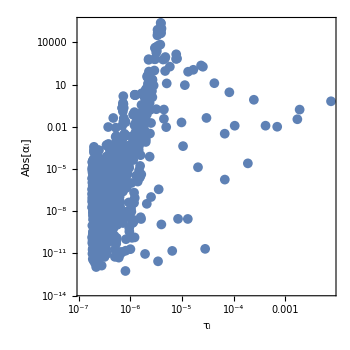
-Graphics- | -Graphics-

fig3.pdf

```mathematica
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
α=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"alpha.npy","Real64"][[17;;-1]],2];

order=Reverse[Ordering[Abs[α]]];
evecs3=evecs[[order]];
angles=Re[(evecs3.ConjugateTranspose[evecs3])/Outer[Times,Norm/@evecs3,Norm/@evecs3]];
dim2=Length[evals];
p=Grid[{{ListLogLogPlot[Transpose[{-1/evals,Abs[α]}][[1;;-2]],PlotRange->All,Axes->False,Frame->True,FrameLabel->{Subscript[τ,i],Abs[Subscript["α",i]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->350,ImagePadding->{{95,25},{75,25}},PlotStyle->Directive[PointSize[0.02]]],Legended[rasterizeBackground[
MatrixPlot[ArcCos[Abs[angles]],ColorFunctionScaling->False,ColorFunction->(Blend[{Blue,Lighter[Yellow]},#/(Pi/2)]&),ClippingStyle->None,PlotRange->{0,Pi/2},ImageSize->350,FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16],FrameLabel->{i,j},FrameTicks->{{Table[Round[i],{i,1,dim2+1,dim2/5}],Table[{Round[i],""},{i,1,dim2+1,dim2/5}]},{Table[Round[i],{i,1,dim2+1,dim2/5}],Table[{Round[i],""},{i,1,dim2+1,dim2/5}]}},ImagePadding->{{95,25},{75,25}},ColorFunction->"TemperatureMap",PlotRange->{0,1},MaxPlotPoints->Infinity]],MatrixPlot[Table[i,{i,0,100},{j,0,100}],ColorFunction->(Blend[{Blue,Lighter[Yellow]},#/(100)]&),ColorFunctionScaling->False,AspectRatio->10,ImageSize->{Automatic,200},FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{{None,Subscript[θ,ij]},{None,None}},FrameTicks->{{None,{{1,0},{26,DisplayForm[RowBox[{Pi,"/",8}]]},{51,DisplayForm[RowBox[{Pi,"/",4}]]},{76,DisplayForm[RowBox[{3Pi,"/",8}]]},{101,DisplayForm[RowBox[{Pi,"/",2}]]}}},{None,None}},DataReversed->True,LabelStyle->Directive[16,Black]]]}}]
Export["fig3.pdf",p]
```

#### fig4

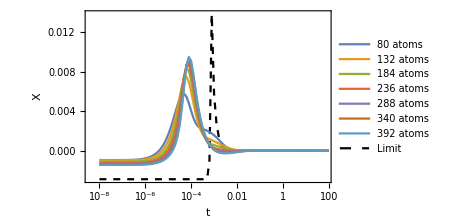

fig4a.pdf

```mathematica
filebase="data/h2o2";
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
concentrations=Transpose[Partition[BinaryReadList[filebase<>"concentrations.npy","Real64"][[17;;-1]],9]];
p0=ListLogLinearPlot[Transpose[{times,concentrations[[2]]+concentrations[[3]]+concentrations[[5]]+concentrations[[7]]-(concentrations[[2,-1]]+concentrations[[3,-1]]+concentrations[[5,-1]]+concentrations[[7,-1]])}],PlotStyle->Directive[Black,Dashed],Axes->False,Frame->True,FrameLabel->{t,X},PlotRange->All,LabelStyle->Directive[Black,16],FrameStyle->Directive[AbsoluteThickness[2],Black],ImageSize->350,Joined->True,PlotRange->All];

t0=10.^-8;
t1=10^2;

rads={};
initials={};
Monitor[Do[filebase="data/dimred3/"<>ToString[i];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
o2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[4]])/Total[#])&/@multiindices)];h2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[1]])/Total[#])&/@multiindices)];
h2onorm=SparseArray[({#,#}&/@Range[dim])->(((#[[6]])/Total[#])&/@multiindices)];
radicalnorm=SparseArray[({#,#}&/@Range[dim])->(((#[[2]]+#[[3]]+#[[5]]+#[[7]])/Total[#])&/@multiindices)];
temperaturenorm=SparseArray[({#,#}&/@Range[dim])->(temperatures)];
pressurenorm=SparseArray[({#,#}&/@Range[dim])->(pressures)];
ind=First@FirstPosition[multiindices,dat[[2]]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
radicals=Transpose[{times,(Total/@(states.radicalnorm))-(Total/@(states.radicalnorm))[[-1]]}];AppendTo[rads,radicals];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,If[spatoms[[i,j]]>1,Subscript[elements[[j]],spatoms[[i,j]]],elements[[j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
(*initial=Total[DeleteCases[If[#[[1]]>0, If[#[[1]]==1,DisplayForm[RowBox[{#[[2]]}]], DisplayForm[RowBox[{#[[1]],#[[2]]}]]]]&/@Transpose[{dat[[2]],spforms}],Null]];*)
initial=ToString[2+6*i+20*i]<>" atoms";
AppendTo[initials,initial];p=Show[p0,ListLogLinearPlot[rads,Axes->False,Frame->True,FrameLabel->{t,"Radicals"},PlotRange->All,LabelStyle->Directive[Black,16],FrameStyle->Directive[16,Black],ImageSize->350,Joined->True,PlotRange->All]];,{i,3,15,2}],{filebase,p}]
Legended[p,Placed[LineLegend[Join[ColorData[97,"ColorList"][[1;;Length[initials]]],{Directive[Black,Dashed]}],Join[initials,{"Limit"}]],Right]]
Export["fig4a.pdf",Legended[p,Placed[LineLegend[Join[ColorData[97,"ColorList"][[1;;Length[initials]]],{Directive[Black,Dashed]}],Join[initials,{"Limit"}]],Right]]]
```

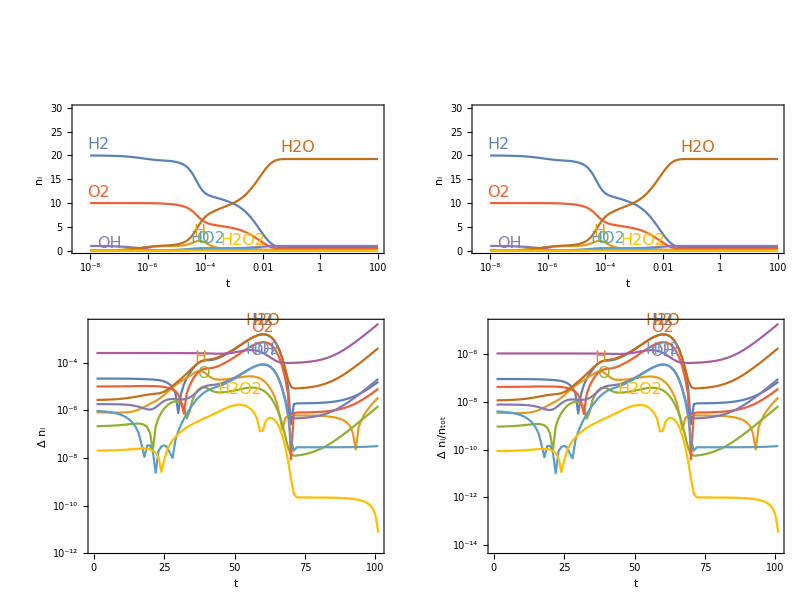

errors.pdf

```mathematica
num=10;
filebase="data/dimred3/"<>ToString[num];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];
elements=dat[[3]];
species={"H2","H","O","O2","OH","H2O","HO2","H2O2","AR"};
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
o2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[4]])/Total[#])&/@multiindices)];h2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[1]])/Total[#])&/@multiindices)];
h2onorm=SparseArray[({#,#}&/@Range[dim])->(((#[[6]])/Total[#])&/@multiindices)];
concentrationnorms=Table[SparseArray[({#,#}&/@Range[dim])->(#[[i]]&/@multiindices)],{i,1,ns}];
temperaturenorm=SparseArray[({#,#}&/@Range[dim])->(temperatures)];
pressurenorm=SparseArray[({#,#}&/@Range[dim])->(pressures)];
ind=First@FirstPosition[multiindices,dat[[2]]];
states1=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
concentrations1=Table[Transpose[{times,(Total/@(states1.concentrationnorms[[i]]))}],{i,1,ns}];
filebase="data/nodimred/"<>ToString[num];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
o2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[4]])/Total[#])&/@multiindices)];h2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[1]])/Total[#])&/@multiindices)];
h2onorm=SparseArray[({#,#}&/@Range[dim])->(((#[[6]])/Total[#])&/@multiindices)];
concentrationnorms=Table[SparseArray[({#,#}&/@Range[dim])->(#[[i]]&/@multiindices)],{i,1,ns}];
temperaturenorm=SparseArray[({#,#}&/@Range[dim])->(temperatures)];
pressurenorm=SparseArray[({#,#}&/@Range[dim])->(pressures)];
ind=First@FirstPosition[multiindices,dat[[2]]];
states2=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
concentrations2=Table[Transpose[{times,(Total/@(states2.concentrationnorms[[i]]))}],{i,1,ns}];
p=Grid[{{ListLogLinearPlot[concentrations1,PlotRange->{0,3*num},ImageSize->350,ImagePadding->{{75,15},{75,75}},Joined->True,PlotLabels->Placed[Table[Style[species[[i]],ColorData[97,"ColorList"][[i]]],{i,1,ns}],Above],Axes->False,Frame->True,FrameLabel->{{Subscript[n,i],None},{t,"Full state space"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]],ListLogLinearPlot[concentrations2,PlotRange->{0,3*num},ImageSize->350,ImagePadding->{{75,15},{75,75}},Joined->True,PlotLabels->Placed[Table[Style[species[[i]],ColorData[97,"ColorList"][[i]]],{i,1,ns}],Above],Axes->False,Frame->True,FrameLabel->{{Subscript[n,i],None},{t,"Dimension reduced"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]},{ListLogPlot[Abs[(concentrations1[[All,All,2]]-concentrations2[[All,All,2]])],PlotRange->All,Joined->True,PlotLabels->Placed[Table[Style[species[[i]],ColorData[97,"ColorList"][[i]]],{i,1,ns}],Above],ImageSize->350,ImagePadding->{{75,15},{75,15}},Axes->False,Frame->True,FrameLabel->{{Δ * Subscript[n,i],None},{t,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]],
ListLogPlot[Transpose[Transpose[Abs[(concentrations1[[All,All,2]]-concentrations2[[All,All,2]])]]/(Total[concentrations1[[All,All,2]]])],PlotRange->All,Joined->True,PlotLabels->Placed[Table[Style[species[[i]],ColorData[97,"ColorList"][[i]]],{i,1,ns}],Above],ImageSize->350,ImagePadding->{{75,15},{75,15}},Axes->False,Frame->True,FrameLabel->{{DisplayForm[RowBox[{Δ * Subscript[n,i],"/",Subscript[n,"tot"]}]],None},{t,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]}}]
Export["errors.pdf",p]
```

```mathematica
Max[Transpose[Transpose[Abs[(concentrations1[[All,All,2]]-concentrations2[[All,All,2]])]]/(Total[concentrations1[[All,All,2]]])]]*100
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
Length[evals]
```

0.00191751

4000

#### fig5

data/nodimred/8

{21717,9,0}

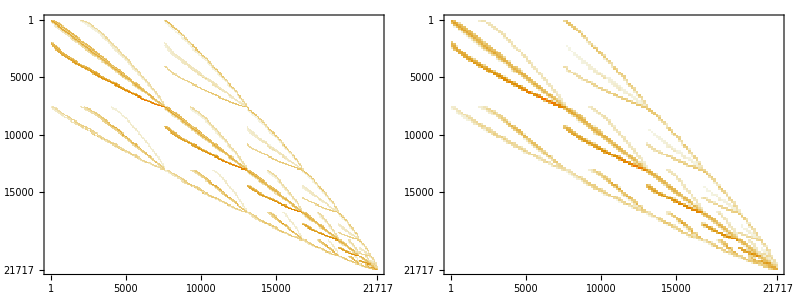

{0.594862,Null}

{0.022233,Null}

2801

{113.54,Null}

{0.069858,Null}

{2742.79,-Graphics-}

{142.871,data/nodimred/8connected.pdf}

```mathematica
filebase="data/nodimred/8"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temp=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pres=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
thrs=10^-3;
vals=A["NonzeroValues"];
pos=A["NonzeroPositions"];
Do[If[A[[pos[[i,1]],pos[[i,2]]]]<thrs*A[[pos[[i,2]],pos[[i,1]]]],vals[[i]]=0],{i,1,Length[pos]}]
A2=SparseArray[#[[1]]->#[[2]]&/@Transpose[{pos,vals}]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,If[spatoms[[i,j]]>1,Subscript[elements[[j]],spatoms[[i,j]]],elements[[j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
Grid[{{MatrixPlot[A],MatrixPlot[A2]}}]

AbsoluteTiming[g=Graph[#[[1]]->#[[2]]&/@A2["NonzeroPositions"]];]
AbsoluteTiming[components=ConnectedComponents[g];]

Length[ConnectedComponents[g]]
Monitor[AbsoluteTiming[edges=Flatten[Table[ParallelTable[If[Max[Abs[A2[[components[[i]],components[[j]]]]]]>0&&i!=j,i->j,{}],{j,1,i}],{i,1,Length[components]}]];],{i}]
AbsoluteTiming[g=Graph[Range[Length[components]],edges,GraphLayout->{"VertexLayout"->"LayeredDigraphEmbedding"},ImageSize->1000,AspectRatio->1/2,VertexSize->0.02*Length[components],PerformanceGoal->"Quality",EdgeStyle->Directive[Opacity[0.5],Arrowheads[0.01]]];]
AbsoluteTiming[p=Show[g]]
AbsoluteTiming[Export[filebase<>"connected.pdf",p]]
(*AbsoluteTiming[vcs=GraphEmbedding[g,{"VertexLayout"->"LayeredDigraphEmbedding","EdgeLayout"->"StraightLine"}];]
{xmax,xmin}={Max[vcs[[All,1]]],Min[vcs[[All,1]]]};
{ymax,ymin}={Max[vcs[[All,2]]],Min[vcs[[All,2]]]};
vcs=Table[{2*vcs[[i,1]]/(xmax-xmin),vcs[[i,2]]/(ymax-ymin)},{i,1,Length[vcs]}];
vsizes=Table[i->0.01,{i,1,dim}];
AbsoluteTiming[Graphics[Join[{Arrowheads[0.005],Directive[Opacity[0.7],Hue[0.6, 0.7, 0.5]],Opacity[0.1]},Table[Arrow[{vcs[[edges[[i,1]]]],vcs[[edges[[i,2]]]]},edges[[i,2]]/.vsizes],{i,1,Length[edges]}],{Opacity[1],Directive[Hue[0.6, 0.2, 0.8],EdgeForm[Directive[GrayLevel[0],Opacity[0.7]]]]},Table[Disk[vcs[[i]],i/.vsizes],{i,1,Length[vcs]}]],ImageSize->1000,AspectRatio->1/2]]*)
```

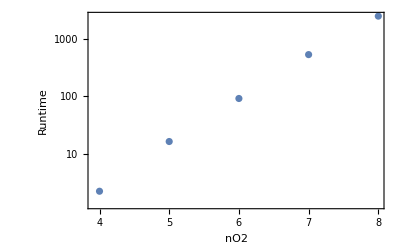

layeredruntimes.pdf

{0.000729413,0.0041622,0.0237505,0.135526,0.773343,4.41288,25.1809}

```mathematica
rtimes={{4,2.291778},{5,16.612563},{6,92.25724},{7,529.975364},{8,2454.775383}};
p=ListLogPlot[rtimes,Axes->False,Frame->True,FrameLabel->{"nO2","Runtime"},LabelStyle->Directive[16,Black]]
Export["layeredruntimes.pdf",p]
Table[1/3600.*10^Fit[{#[[1]],Log[#[[2]]]/Log[10]}&/@rtimes,{1,x},x]/.x->X,{X,4,10}]
```

data/dimred3/10

{11106,9,0}

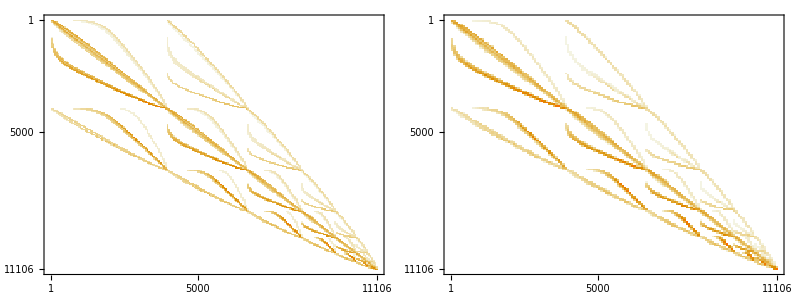

{0.321582,Null}

{0.010627,Null}

10

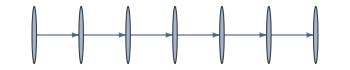

```mathematica
filebase="data/dimred3/10"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temp=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pres=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
thrs=10^-3;
vals=A["NonzeroValues"];
pos=A["NonzeroPositions"];
Do[If[A[[pos[[i,1]],pos[[i,2]]]]<thrs*A[[pos[[i,2]],pos[[i,1]]]],vals[[i]]=0],{i,1,Length[pos]}]
A2=SparseArray[#[[1]]->#[[2]]&/@Transpose[{pos,vals}]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,If[spatoms[[i,j]]>1,Subscript[elements[[j]],spatoms[[i,j]]],elements[[j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
Grid[{{MatrixPlot[A],MatrixPlot[A2]}}]

AbsoluteTiming[g=Graph[#[[1]]->#[[2]]&/@A2["NonzeroPositions"]];]
AbsoluteTiming[components=ConnectedComponents[g];]

Length[ConnectedComponents[g]]
componentprob=Table[Total[states[[i,components[[j]]]]],{i,1,Length[states]},{j,1,Length[components]}];
maxes=Max/@
Transpose[componentprob];
components=Extract[components,Position[maxes,u_/;Abs[u]>10^-8]];
vsizes=Table[i->2*Length[components]*(0.01+0.05*N[Length[components[[i]]]/dim]^(1/2)),{i,1,Length[components]}];
vstyles=Table[i->If[MemberQ[components[[i]],First@FirstPosition[multiindices,dat[[2]]]],Black,White],{i,1,Length[components]}];

g=Graph[Range[Length[components]],Flatten[Table[If[Max[Abs[A2[[components[[i]],components[[j]]]]]]>0&&i!=j,i->j,{}],{i,1,Length[components]},{j,1,Length[components]}]]];
p=GraphPlot[g,ImageSize->350]
```

```mathematica
Nt=Length[states];
species={"H2","H","O","O2","OH","H2O","HO2","H2O2","AR"};
componentprob=Table[Total[states[[i,components[[j]]]]],{i,1,Length[states]},{j,1,Length[components]}];
maxes=Max/@
Transpose[componentprob];
ptimes=(First/@Position[componentprob,#]&/@maxes)[[All,1]];
complayers=Round[LayeredGraphPlot[g,Left,VertexSize->vsizes,VertexStyle->Table[i->cf[ptimes[[i]]],{i,1,Length[components]}],ImageSize->400,ImagePadding->{{75,15},{75,15}}][[1,1,1;;Length[components],1]]];
layers=Sort[DeleteDuplicates[complayers]];
ptimes[[First@FirstPosition[complayers,0]]]=Nt;
compconcentrations=Transpose[Table[Mean[N[#[[i]]]&/@multiindices[[Flatten[Extract[components,Position[complayers,lay]]]]]],{lay,layers},{i,1,ns}]];
compconcentrations=Transpose[Table[maxes=Max/@Transpose[states[[All,Flatten[Extract[components,Position[complayers,lay]]]]]];
comp=N[#[[i]]]&/@multiindices[[Flatten[Extract[components,Position[complayers,lay]]]]];
Total[maxes/Total[maxes]*comp],{lay,Sort[layers]},{i,1,ns}]];
First@FirstPosition[complayers,1-Length[layers]]
First@FirstPosition[complayers,2-Length[layers]]
First@FirstPosition[complayers,4-Length[layers]]
First@FirstPosition[complayers,0]
```

7

6

4

1

```mathematica
p1=LayeredGraphPlot[g,Left,VertexSize->vsizes,VertexStyle->Table[i->cf[ptimes[[i]]],{i,1,Length[components]}],ImageSize->500,ImagePadding->{{75,75},{5,5}}]/.Arrow[{i_,j_},u_]:>Arrow[{i,j},0.5*{i/.vsizes,j/.vsizes}]/.Arrow[BezierCurve[l_],u_]:>Arrow[BezierCurve[l],0.5*{l[[1]]/.vsizes,l[[-1]]/.vsizes}];
p2=Show[ListPlot[compconcentrations,Joined->True,Axes->False,Frame->True,FrameLabel->{"Layer",Subscript[n,i]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{0.75,Length[layers]+0.25},{-1,21}},FrameTicks->{{Table[i,{i,0,20,5}],Table[{i,""},{i,0,20,5}]},{Table[i,{i,1,Length[layers],2}],Table[{i,""},{i,1,Length[layers],2}]}},PlotLabels->Table[Style[species[[i]],ColorData[97,"ColorList"][[i]]],{i,1,Length[species]}],ImageSize->500,ImagePadding->{{75,75},{75,15}},AspectRatio->2/3],ListPlot[compconcentrations,Joined->False,PlotStyle->Directive[PointSize[0.03]]]];
p=Grid[{{Show[p0,ImageSize->{Automatic,400}],Grid[{{cb1},{p1},{p2}}]}}]
Export["fig5.pdf",p]
```

-Graphics- | -Graphics-

fig5.pdf

#### Create CSVs

```mathematica
filebase="data/nodimred/10";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
Export[filebase<>"rows.csv",Transpose[{rows}]]
Export[filebase<>"columns.csv",Transpose[{columns}]]
Export[filebase<>"data.csv",Transpose[{data}]]
Export[filebase<>"w_sparse.csv",Transpose[{rows,columns,data}]]
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
Export[filebase<>"states.csv",states]
```

{63835,9,0}

data/nodimred/10rows.csv

data/nodimred/10columns.csv

data/nodimred/10data.csv

data/nodimred/10w_sparse.csv

#### fig6

```mathematica
filebase="data/dimred3/10"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temp=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pres=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
thrs=10^-3;
vals=A["NonzeroValues"];
pos=A["NonzeroPositions"];
Do[If[A[[pos[[i,1]],pos[[i,2]]]]<thrs*A[[pos[[i,2]],pos[[i,1]]]],vals[[i]]=0],{i,1,Length[pos]}]
A2=SparseArray[#[[1]]->#[[2]]&/@Transpose[{pos,vals}]];
AbsoluteTiming[edges2=#[[1]]->#[[2]]&/@A2["NonzeroPositions"];]
AbsoluteTiming[g=Graph[Range[dim],edges2];]
AbsoluteTiming[vcs=GraphEmbedding[g,{"VertexLayout"->"SpringElectricalEmbedding","EdgeLayout"->"StraightLine"}];]
AbsoluteTiming[vsizes=Table[0.02+0.5*states[[-1,i]],{i,1,dim}];]
Dimensions[Max/@Transpose[states]]
show=First/@Position[Max/@Transpose[states],u_/;Abs[u]>10^-8];
Length[show]
AbsoluteTiming[edges3=Flatten[If[MemberQ[show,#[[1]]]&&MemberQ[show,#[[2]]],#[[1]]->#[[2]],{}]&/@A2["NonzeroPositions"]];]
AbsoluteTiming[g=Graph[show,edges3];]
AbsoluteTiming[vcs=GraphEmbedding[g,{"VertexLayout"->"SpringElectricalEmbedding","EdgeLayout"->"StraightLine"}];]
{xmax,xmin}={Max[vcs[[All,1]]],Min[vcs[[All,1]]]};
{ymax,ymin}={Max[vcs[[All,2]]],Min[vcs[[All,2]]]};
vcs=10*{2*#[[1]]/(xmax-xmin),#[[2]]/(ymax-ymin)}&/@vcs;
vsizes=Table[0.02+0.5*states[[-1,i]],{i,show}];
AbsoluteTiming[g=Graph[Range[dim],edges2];]
components=ConnectedComponents[g];
componentprob=Table[Total[states[[i,components[[j]]]]],{i,1,Length[states]},{j,1,Length[components]}];
maxes=Max/@
Transpose[componentprob];
components=Intersection[show,#]&/@Reverse[Extract[components,Position[maxes,u_/;Abs[u]>10^-8]]];
```

data/dimred3/10

{11106,9,0}

{0.234298,Null}

{0.091491,Null}

{3.14792,Null}

{0.097598,Null}

{11106}

1819

{16.1929,Null}

{0.037943,Null}

{0.473843,Null}

{0.080737,Null}

{112.493,Null}

{2.66455,Null}

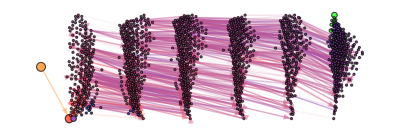

fig6.pdf

```mathematica
vcs2={};
x0=0;
dx=1.5;
dy=3;
orientations=ConstantArray[1,Length[components]];
orientations[[2]]=-1;
orientations[[3]]=-1;
Do[
emb=Reverse/@GraphEmbedding[Graph[components[[cid]],Cases[edges3,u_/;MemberQ[components[[cid]],u[[1]]]&&MemberQ[components[[cid]],u[[2]]]]]];
If[orientations[[cid]]==-1,emb={-#[[1]],-#[[2]]}&/@emb,emb={-#[[1]],#[[2]]}&/@emb];
{xmax,xmin}={Max[emb[[All,1]]],Min[emb[[All,1]]]};
{ymax,ymin}={Max[emb[[All,2]]],Min[emb[[All,2]]]};
If[xmax>xmin&&ymax>ymin,emb={dx*cid+(#[[1]]-xmin)/(xmax-xmin),dy*(#[[2]]-ymin)/(ymax-ymin)}&/@emb;,emb={dx*cid+dx/2,dy/2}&/@emb;];
vcs2=Join[vcs2,Table[components[[cid,i]]->emb[[i]],{i,1,Length[emb]}]];,{cid,1,Length[components]}]
vcs3=show/.vcs2;
maxes2=Max[states[[All,#]]]&/@show;
ptimes2=First@FirstPosition[states[[All,#]],maxes2[[First@FirstPosition[show,#]]]]&/@show;
ptimes2=ptimes2/.u_/;u>70:>Nt;
vsizes2=Table[(0.03+0.1*maxes2[[i]]),{i,1,Length[show]}];
vstyles=Table[cf[ptimes2[[i]]],{i,1,Length[show]}];
AbsoluteTiming[Monitor[fluxes=Table[Abs[A2[[#[[1]],#[[2]]]]*states[[nt,#[[1]]]]-A2[[#[[2]],#[[1]]]]*states[[nt,#[[2]]]]]/10^1&/@edges2,{nt,1,100}];,nt]]
maxfluxes=Max/@Transpose[fluxes];
AbsoluteTiming[Monitor[fluxtimes=Table[First@FirstPosition[fluxes[[All,i]],maxfluxes[[i]]],{i,1,Length[maxfluxes]}];,i]]
p=Graphics[Join[{Arrowheads[0.007],Directive[Opacity[0.7],Hue[0.6,0.7,0.5]],Opacity[0.1]},{Opacity[Min[0.5,maxfluxes[[#]]/10^1]],cf[fluxtimes[[#]]],Arrow[{vcs3[[First@FirstPosition[show,edges3[[#,1]]]]],vcs3[[First@FirstPosition[show,edges3[[#,2]]]]]},Max[0,vsizes2[[First@FirstPosition[show,edges3[[#,2]]]]]]]}&/@Range[Length[edges3]],{Opacity[1],Directive[Hue[0.6,0.2,0.8],EdgeForm[Directive[GrayLevel[0],Opacity[0.7]]]]},{vstyles[[#]],Disk[vcs3[[#]],vsizes2[[#]]]}&/@Range[Length[show]]],ImageSize->{Automatic,500},ImagePadding->{{ImageScaled[0.05],ImageScaled[0.05]},{ImageScaled[0.05],ImageScaled[0.05]}}]
Export["fig6.pdf",p]
```

### animation

```mathematica
filebase="data/dimred3/10"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temp=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pres=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
thrs=10^-3;
vals=A["NonzeroValues"];
pos=A["NonzeroPositions"];
Do[If[A[[pos[[i,1]],pos[[i,2]]]]<thrs*A[[pos[[i,2]],pos[[i,1]]]],vals[[i]]=0],{i,1,Length[pos]}]
A2=SparseArray[#[[1]]->#[[2]]&/@Transpose[{pos,vals}]];
AbsoluteTiming[edges2=#[[1]]->#[[2]]&/@A2["NonzeroPositions"];]
AbsoluteTiming[g=Graph[Range[dim],edges2];]
AbsoluteTiming[vcs=GraphEmbedding[g,{"VertexLayout"->"SpringElectricalEmbedding","EdgeLayout"->"StraightLine"}];]
AbsoluteTiming[vsizes=Table[0.02+0.5*states[[-1,i]],{i,1,dim}];]
```

data/dimred3/10

{11106,9,0}

{0.224967,Null}

{0.074437,Null}

{3.32176,Null}

{0.096329,Null}

```mathematica
Dimensions[Max/@Transpose[states]]
show=First/@Position[Max/@Transpose[states],u_/;Abs[u]>10^-8];
Length[show]
AbsoluteTiming[edges3=Flatten[If[MemberQ[show,#[[1]]]&&MemberQ[show,#[[2]]],#[[1]]->#[[2]],{}]&/@A2["NonzeroPositions"]];]
AbsoluteTiming[g=Graph[show,edges3];]
AbsoluteTiming[vcs=GraphEmbedding[g,{"VertexLayout"->"SpringElectricalEmbedding","EdgeLayout"->"StraightLine"}];]
{xmax,xmin}={Max[vcs[[All,1]]],Min[vcs[[All,1]]]};
{ymax,ymin}={Max[vcs[[All,2]]],Min[vcs[[All,2]]]};
vcs=10*{2*#[[1]]/(xmax-xmin),#[[2]]/(ymax-ymin)}&/@vcs;
vsizes=Table[0.02+0.5*states[[-1,i]],{i,show}];
```

{11106}

1819

{17.1193,Null}

{0.031042,Null}

{0.449082,Null}

{0.097743,Null}

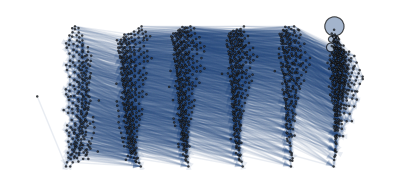

```mathematica
AbsoluteTiming[g=Graph[Range[dim],edges2];]
components=ConnectedComponents[g];
componentprob=Table[Total[states[[i,components[[j]]]]],{i,1,Length[states]},{j,1,Length[components]}];
maxes=Max/@
Transpose[componentprob];
components=Intersection[show,#]&/@Reverse[Extract[components,Position[maxes,u_/;Abs[u]>10^-8]]];

vcs2={};
x0=0;
dx=1.5;
dy=4;
orientations=ConstantArray[1,Length[components]];
orientations[[2]]=-1;
orientations[[3]]=-1;
Do[
emb=Reverse/@GraphEmbedding[Graph[components[[cid]],Cases[edges3,u_/;MemberQ[components[[cid]],u[[1]]]&&MemberQ[components[[cid]],u[[2]]]]]];
If[orientations[[cid]]==-1,emb={-#[[1]],-#[[2]]}&/@emb,emb={-#[[1]],#[[2]]}&/@emb];
{xmax,xmin}={Max[emb[[All,1]]],Min[emb[[All,1]]]};
{ymax,ymin}={Max[emb[[All,2]]],Min[emb[[All,2]]]};
If[xmax>xmin&&ymax>ymin,emb={dx*cid+(#[[1]]-xmin)/(xmax-xmin),dy*(#[[2]]-ymin)/(ymax-ymin)}&/@emb;,emb={dx*cid+dx/2,dy/2}&/@emb;];
vcs2=Join[vcs2,Table[components[[cid,i]]->emb[[i]],{i,1,Length[emb]}]];,{cid,1,Length[components]}]
vcs3=show/.vcs2;
Graphics[Join[{Arrowheads[0.007],Directive[Opacity[0.7],Hue[0.6,0.7,0.5]],Opacity[0.1]},Arrow[{vcs3[[First@FirstPosition[show,#[[1]]]]],vcs3[[First@FirstPosition[show,#[[2]]]]]},Max[0,vsizes[[First@FirstPosition[show,#[[2]]]]]]]&/@edges3,{Opacity[1],Directive[Hue[0.6,0.2,0.8],EdgeForm[Directive[GrayLevel[0],Opacity[0.7]]]]},Disk[vcs3[[First@FirstPosition[show,#]]],vsizes[[First@FirstPosition[show,#]]]]&/@show],ImageSize->{Automatic,500},ImagePadding->{{ImageScaled[0.05],ImageScaled[0.05]},{ImageScaled[0.05],ImageScaled[0.05]}}]
```

{2.25,11.5}

{0.,4.}

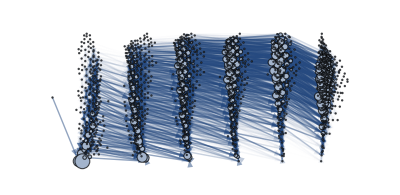

```mathematica
nt=40;
{xmin,xmax}={Min[vcs3[[All,1]]],Max[vcs3[[All,1]]]}
{ymin,ymax}={Min[vcs3[[All,2]]],Max[vcs3[[All,2]]]}
vsizes=Table[0.02+0.1*Log[Max[states[[nt,i]],10^-4]/10^-4]/4,{i,show}];
Graphics[Join[{Arrowheads[0.007],Directive[Opacity[0.7],Hue[0.6,0.7,0.5]],Opacity[0.5]},{Opacity[Min[0.5,Abs[A2[[#[[1]],#[[2]]]]*states[[nt,#[[1]]]]-A2[[#[[2]],#[[1]]]]*states[[nt,#[[2]]]]]/10^1]],Arrow[{vcs3[[First@FirstPosition[show,#[[1]]]]],vcs3[[First@FirstPosition[show,#[[2]]]]]},{0,Max[0,vsizes[[First@FirstPosition[show,#[[2]]]]]]}]}&/@edges3,{Opacity[1],Directive[Hue[0.6,0.2,0.8],EdgeForm[Directive[GrayLevel[0],Opacity[0.7]]]]},Disk[vcs3[[First@FirstPosition[show,#]]],vsizes[[First@FirstPosition[show,#]]]]&/@show],ImageSize->{Automatic,500},ImagePadding->{{ImageScaled[0.05],ImageScaled[0.05]},{ImageScaled[0.05],ImageScaled[0.05]}},PlotRange->{{xmin-1/2,xmax+1/2},{ymin-1/2,ymax+1/2}}]
```

```mathematica
AbsoluteTiming[ParallelDo[vsizes=Table[0.02+0.1*Log[Max[states[[nt,i]],10^-4]/10^-4]/4,{i,show}];
plot=Graphics[Join[{Arrowheads[0.007],Directive[Opacity[0.7],Hue[0.6,0.7,0.5]],Opacity[0.5]},{If[Abs[A2[[#[[1]],#[[2]]]]*(states[[nt,#[[1]]]])]<1,Opacity[0],Opacity[Abs[A2[[#[[1]],#[[2]]]]*states[[nt,#[[1]]]]-A2[[#[[2]],#[[1]]]]*states[[nt,#[[2]]]]]/10^2]],Arrow[{vcs3[[First@FirstPosition[show,#[[1]]]]],vcs3[[First@FirstPosition[show,#[[2]]]]]},{0,Max[0,vsizes[[First@FirstPosition[show,#[[2]]]]]]}]}&/@edges3,{Opacity[1],Directive[Hue[0.6,0.2,0.8],EdgeForm[Directive[GrayLevel[0],Opacity[0.7]]]]},Disk[vcs3[[First@FirstPosition[show,#]]],vsizes[[First@FirstPosition[show,#]]]]&/@show],ImageSize->{Automatic,500},ImagePadding->{{ImageScaled[0.05],ImageScaled[0.05]},{ImageScaled[0.05],ImageScaled[0.05]}},PlotRange->{{xmin-1/2,xmax+1/2},{ymin-1/2,ymax+1/2}}];
Export["animation/"<>IntegerString[nt,10,4]<>".png",plot,ImageSize->1000];,{nt,1,100}]]
```

### Rate equations

```mathematica
filebase="data/combustionoh";
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
concentrations=Transpose[Partition[BinaryReadList[filebase<>"concentrations.npy","Real64"][[17;;-1]],9]];
rates=Transpose[Partition[BinaryReadList[filebase<>"rates.npy","Real64"][[17;;-1]],28]];
rstois=Transpose[Partition[BinaryReadList[filebase<>"rstois.npy","Integer64"][[17;;-1]],28]];
pstois=Transpose[Partition[BinaryReadList[filebase<>"pstois.npy","Integer64"][[17;;-1]],28]];
species={"H2","H","O","O2","OH","H2O","HO2","H2O2","AR"};
sptime[text_]:=First@FirstPosition[Accumulate[10^-12+concentrations[[First@FirstPosition[species,text]]]]/Total[10^-12+concentrations[[First@FirstPosition[species,text]]]],u_/;u>0.5]/Nt
sptimemin=Min[sptime/@species];
sptimemax=Max[sptime/@species];
spcol[text_]:=Blend[{Cyan,Orange},(sptime[text]-sptimemin)/(sptimemax-sptimemin)]
nreactions=Length[rstois];
Nt=Length[concentrations[[1]]];
tint=Interpolation[Transpose[{Range[Nt]/Nt,times}]];
reactants=Table[Extract[species,Position[rstois[[i]],u_/;u>0]],{i,1,nreactions}];
products=Table[Extract[species,Position[pstois[[i]],u_/;u>0]],{i,1,nreactions}];
```

```mathematica
Nt=Length[times];
Tmax=Max[temperatures];
Tmin=Min[temperatures];
Pmax=Max[pressures];
Pmin=Min[pressures];
imagePadding2={{75,75},{1,1}};
imgSize2={500,250};
imagePadding1={{75,75},{50,1}};
imgSize1={500,290};
imgSize3={440*(2.2)/(1.3),440};
tmax=times[[-1]]
reactantnames={"H2","O2","AR"};
productnames={"H2O2","H2O"};
ohintermediates={"H2","H","O","OH","HO2"};
nspecies=Length[species]
cmax=1.1*Max[{concentrations[[First@FirstPosition[species,"H2O"]]],concentrations[[First@FirstPosition[species,"H2"]]][[2]],concentrations[[First@FirstPosition[species,"O2"]]][[2]]}];
cplots={"H2","O2","H2O"};
ccplots=ColorData[97,"ColorList"][[1;;3]];
p1=ListLogPlot[Join[concentrations,(concentrations[[First@FirstPosition[species,#]]])&/@cplots],Joined->True,PlotRange->{10^-12,1},LabelStyle->Directive[16,Black],Axes->False,Frame->True,FrameLabel->{None,DisplayForm[RowBox[{"Mole Fraction,",Subscript[ X,i]}]]},FrameTicks->{{Automatic,{}},Table[{i,""},{i,0,(Nt-1),(Nt-1)/5}]},PlotStyle->Join[ConstantArray[Directive[Thickness[0.005],LightGray],nspecies],Directive[Thickness[0.01],#]&/@ccplots],FrameStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRangeClipping->False,ImagePadding->imagePadding2,ImageSize->imgSize2];
p2=ListPlot[{(temperatures-Tmin)/(Tmax-Tmin)+0.05,(pressures-Pmin)/(Pmax-Pmin)-0.05},Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[4]],Thickness[0.01]],Directive[ColorData[97,"ColorList"][[5]],Thickness[0.01]]},PlotRange->{-0.1,1.1},LabelStyle->Directive[16,Black],Axes->False,Frame->True,FrameLabel->{{Style["Temperature (K)",ColorData[97,"ColorList"][[4]]],Style["Pressure (atm)",ColorData[97,"ColorList"][[5]]]},{"Time (ms)",None}},FrameTicks->{{Table[{(T-Tmin)/(Tmax-Tmin),Style[Round[T],ColorData[97,"ColorList"][[4]]]},{T,Tmin,Tmax,(Tmax-Tmin)/3}],Table[{(P-Pmin)/(Pmax-Pmin),Style[PaddedForm[P,{3,2}],ColorData[97,"ColorList"][[5]]]},{P,Pmin,Pmax,(Pmax-Pmin)/3}]},{Table[{i,tint[(i-1)/Nt]/10^-3},{i,2,Length[times]+1,Round[Length[times]/5]}],{}}},FrameStyle->Directive[Black,AbsoluteThickness[1.5]],ImagePadding->imagePadding1,ImageSize->imgSize1];
```

79.4328

9

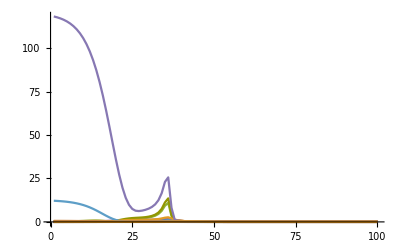

```mathematica
ListPlot[Abs[rates],PlotRange->All,Joined->True]
```

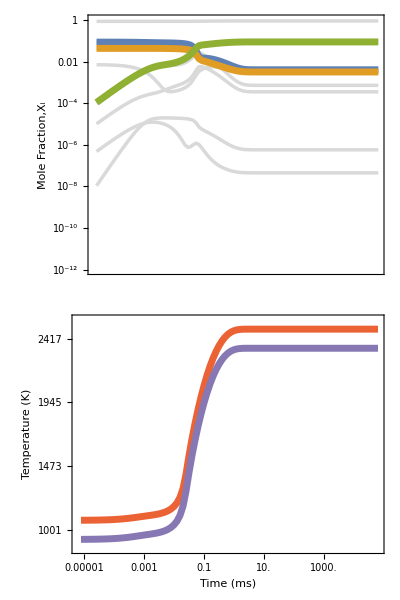
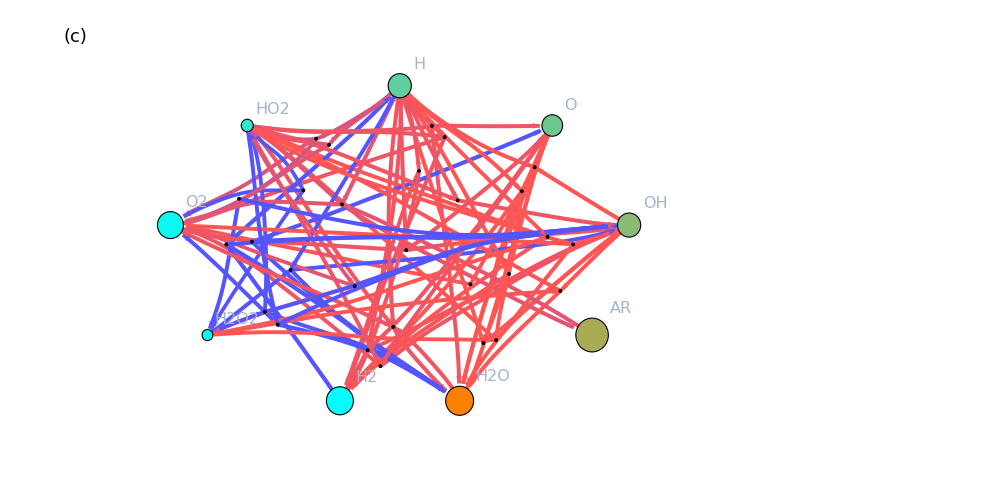
-Graphics- | -Graphics-

h2o2bipartite.pdf

```mathematica
r1=1.5;
r2=1;
colors={Lighter[Blue],Lighter[Red]};
weights=Mean/@rates;
weights2=First@FirstPosition[Abs[#],Max[Abs[#]]]&/@rates/Nt;
wscale=Max[Abs[weights]];
ethrs=10^-64;
ethick=0.003;
shown=Flatten[Position[weights,u_/;Abs[u]>ethrs]];
edges=Table[If[weights[[i]]>0,Join[Table[reactants[[i,j]]->i,{j,1,Length[reactants[[i]]]}],Table[i->products[[i,j]],{j,1,Length[products[[i]]]}]],Join[Table[i->reactants[[i,j]],{j,1,Length[reactants[[i]]]}],Table[products[[i,j]]->i,{j,1,Length[products[[i]]]}]]],{i,1,nreactions}];
vertices=Union[species,DeleteDuplicates[Flatten[edges][[All,1]],Flatten[edges][[All,2]]]];
center=DeleteDuplicates[Join[Flatten[edges[[shown,All,1]]],Flatten[edges[[shown,All,2]]]]];
centerspecies=SortBy[Complement[DeleteDuplicates[DeleteDuplicates[Join[Flatten[edges[[shown,All,1]]],Flatten[edges[[shown,All,2]]]]]],Range[nreactions]],spcol[#]&];
centerreactions=Complement[center,centerspecies];
bottomspecies=SortBy[Complement[species,centerspecies],spcol[#]&];
bottomreactions=Complement[Range[nreactions],centerreactions];
rvcs=GraphEmbedding[PathGraph[Flatten[Position[weights,u_/;Abs[u]>ethrs]],GraphLayout->"SpiralEmbedding"]];
rvcs2=GraphEmbedding[PathGraph[Flatten[Position[weights,u_/;Abs[u]<=ethrs]],GraphLayout->"SpiralEmbedding"]];
{xmax,xmin,ymax,ymin}={Max[rvcs[[All,1]]],Min[rvcs[[All,1]]],Max[rvcs[[All,2]]],Min[rvcs[[All,2]]]};
{xmax2,xmin2,ymax2,ymin2}={Max[rvcs2[[All,1]]],Min[rvcs2[[All,1]]],Max[rvcs2[[All,2]]],Min[rvcs2[[All,2]]]};
transform[p_]:=1.5*{r1,r2}*{(p[[2]]-ymin)/(ymax-ymin)-1/2,(p[[1]]-xmin)/(xmax-xmin)-1/2};
transform2[p_]:=1.5*{r1,r2}*{(p[[2]]-ymin2)/(ymax2-ymin2)-1/2,(p[[1]]-xmin2)/(xmax2-xmin2)-1/2};
trange=Quantile[Extract[weights2,Position[weights,u_/;Abs[u]>ethrs]],{0.25,0.75}];
eweight[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights[[edge[[1]]]],weights[[edge[[2]]]]];
ecolor[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights2[[edge[[1]]]],weights2[[edge[[2]]]]];
vsize[text_]:=0.005+0.08*(Log[Max[Mean[concentrations[[First@FirstPosition[species,text]]]],10^-8]]/Log[10]+8)/8;
sizes={1.0,0.1,0.01,0.001,0.0001};
wsizes=Table[z/.First@Solve[(Log[Abs[z/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])==i*1.0/5,z],{i,5,1,-1}];
vcs=Join[Table[centerspecies[[i]]->{r1*Cos[3*Pi/2-Pi/12-(2*Pi-2*Pi/12)*(i-1)/(Length[centerspecies]-1)],r2*Sin[3*Pi/2-Pi/12-(2*Pi-2*Pi/12)*(i-1)/(Length[centerspecies]-1)]},{i,1,Length[centerspecies]}],
Table[bottomspecies[[i]]->{0,-r2},{i,1,Length[bottomspecies]}],Table[i->If[MemberQ[centerreactions,i],transform[rvcs[[First@FirstPosition[SortBy[Flatten[Position[weights,u_/;Abs[u]>ethrs]],weights2[[#]]&],i]]]],transform2[rvcs2[[First@FirstPosition[SortBy[Flatten[Position[weights,u_/;Abs[u]<=ethrs]],weights2[[#]]&],i]]]]],{i,nreactions}]];
p0=Graph[vertices,Flatten[edges],GraphLayout->{"EdgeLayout"->"DividedEdgeBundling"},VertexCoordinates->vcs,VertexLabels->(#->If[IntegerQ[#],"",Style[#,16]]&/@vertices),VertexStyle->(#->If[ValueQ[Element[#,Integers]],{If[MemberQ[bottomreactions,#],{Opacity[0],EdgeForm[None]},{Opacity[1],EdgeForm[Black]}],Black},If[MemberQ[centerspecies,#],{spcol[#],EdgeForm[Black]},{Opacity[1.0],Blend[spcol/@bottomspecies],EdgeForm[Black]}]]&/@vertices),
VertexSize->(#->If[ValueQ[Element[#,Integers]],{"Scaled",0.005},If[MemberQ[centerspecies,#],{"Scaled",0.7*vsize[#]},{"Scaled",0.7*Mean[vsize/@bottomspecies]}]]&/@vertices),EdgeStyle->(#-> If[Abs[eweight[#]]<=ethrs,{Directive[Opacity[0]]},{Directive[Opacity[1.0]],Directive[Blend[colors,(ecolor[#]-trange[[1]])/(trange[[2]]-trange[[1]])]],Thickness[Abs[ethick*(Log[Abs[eweight[#]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])]],Arrowheads[{{Abs[10*ethick*(Log[Abs[eweight[#]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])],1.0}}]}]&/@Flatten[edges]),EdgeShapeFunction->(If[Position[vcs,First[#]]≠{},{Arrow[#,{0.0,1.5*vsize[vcs[[FirstPosition[N[vcs],Last[#]][[1]],1]]]}]},{Arrow[#,{0.0,0.01}]}]&),ImageSize->{1000,500}];
p=Show[p0,Prolog->{Inset[Grid[{{Graphics[Text[Style["Nodes",16],{0,0}],ImageSize->{125,50}],Graphics[Text[Style["Links",16],{0,0}],ImageSize->{125,50}]},{MatrixPlot[Table[Blend[{Cyan,Orange},(y-sptimemin)/(sptimemax-sptimemin)],{y,sptimemin,sptimemax,(sptimemax-sptimemin)/100},{x,1,100}],AspectRatio->10,ImageSize->{125,175},ImagePadding->{{90,15},{10,5}},FrameTicks->{{Table[{i,PaddedForm[tint[(sptimemin+(i-1)*(sptimemax-sptimemin)/100)]/10^-3,{3,2}]},{i,1,101,20}],None},{None,None}},PlotRangePadding->None,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{"Species Time (ms)",None}},RotateLabel->True,DataReversed->{True,True}],
MatrixPlot[Table[Directive[Opacity[1.0],Blend[colors,(y-trange[[1]])/(trange[[2]]-trange[[1]])]],{y,trange[[1]],trange[[2]],(trange[[2]]-trange[[1]])/100},{x,1,100}],AspectRatio->10,ImageSize->{125,175},ImagePadding->{{5,90},{10,5}},FrameTicks->{{None,Table[{i,PaddedForm[tint[(trange[[1]]+(i-1)*(trange[[2]]-trange[[1]])/100)]/10^-3,{3,2}]},{i,1,101,20}]},{None,None}},PlotRangePadding->None,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{None,"Reaction Time (ms)"}},RotateLabel->True,DataReversed->{True,True}]},{Graphics[{{Table[{EdgeForm[Black],White,Disk[{-1.0,-1.25*i},12*(0.005+0.08*(Log[sizes[[i]]]/Log[10]+8)/8)],Black,Text[Style[With[{n=i},HoldForm[10^(-n)]],16],{-2.8,-1.25*i}]},{i,1,Length[sizes]}]},Rotate[Text[Style["Mole Fraction",16],{-4.0,-4}],Pi/2]},PlotRange->{{-5,0.1},{-8,0}},ImageSize->{125,175}],Graphics[{{Table[{Thickness[10*Abs[ethick*(Log[Abs[wsizes[[i]]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])]],Line[{{1,-1.25*i},{2,-1.25*i}}],Text[Style[PaddedForm[wsizes[[i]],{2,2}],16],{3,-1.25*i}]},{i,1,Length[sizes]}]},Rotate[Text[Style[DisplayForm[RowBox[{"Rate ","(","mol ",Superscript["m",-3],Superscript["ms",-1],")"}]],16],{4.9,-4}],Pi/2]},PlotRange->{{0.5,6},{-8,0}},ImageSize->{125,175}]}}],{2.6,0.0}]},ImageSize->{1000,500},PlotRange->{{-2,3.3},{-1.3,1.25}},PlotRangePadding->None];
p3=Grid[{{Grid[{{Show[p1,Epilog->{Inset[Style["(a)",18],ImageScaled[{0,1}],Scaled[{0,1}]]},PlotRangeClipping->False]},{Show[p2,Epilog->{Inset[Style["(b)",18],ImageScaled[{0,1}],Scaled[{0,1}]]},PlotRangeClipping->False]}},Alignment->Left,Spacings->0],Show[p,Epilog->{Inset[Style["(c)",18],Scaled[{0,1}],Scaled[{0,1}]]}]}},Spacings->0]
Export["h2o2bipartite.pdf",p3]
```

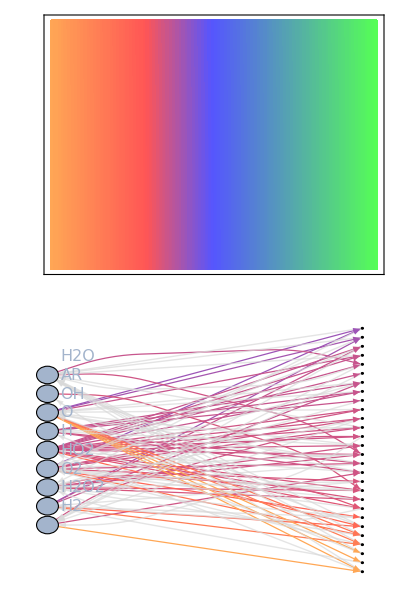

bipartitie1.pdf

```mathematica
weights2=First@FirstPosition[Abs[#],Max[Abs[#]]]&/@rates;
ecolor[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights2[[edge[[1]]]],weights2[[edge[[2]]]]]
cf[tind_]:=Piecewise[{{LightGray,tind<0},{Blend[{c1,c2},(tind-tind0)/(tind1-tind0)],tind<=tind1},{Blend[{c2,c3},(tind-tind1)/(tind2-tind1)],tind≤tind2},{Blend[{c3,c4},(tind-tind2)/(tind3-tind2)],tind>tind2}}];
p0=Graph[Flatten[{SortBy[species,sptime],SortBy[Range[Length[edges]],ecolor[edges[[#,1]]]&]}],Flatten[edges],GraphLayout->"BipartiteEmbedding",VertexLabels->(#->If[IntegerQ[#],"",Style[#,16]]&/@vertices),VertexStyle->(#->If[ValueQ[Element[#,Integers]],{If[MemberQ[bottomreactions,#],{Opacity[0],EdgeForm[None]},{Opacity[1],EdgeForm[Black]}],Black},{Opacity[1.0],Hue[0.6,0.2,0.8],EdgeForm[Black]}]&/@vertices),
VertexSize->(#->If[ValueQ[Element[#,Integers]],{"Scaled",0.005},If[MemberQ[centerspecies,#],{"Scaled",0.05},{"Scaled",0.05}]]&/@vertices),EdgeStyle->(#-> If[IntegerQ[#[[1]]],{LightGray},{Directive[Opacity[1.0]],Directive[cf[ecolor[#]]],Thickness[ethick],Arrowheads[{{Abs[10*ethick],1.0}}]}]&/@Flatten[edges]),EdgeShapeFunction->((If[#[[1,1]]>#[[2,1]],{Arrow[#,{0.0,0.075}]},{Arrow[#,{0.0,0.015}]}])&),ImageSize->{300,Automatic}];
p=Grid[{{cb1},{p0}}]
Export["bipartitie1.pdf",p]
```

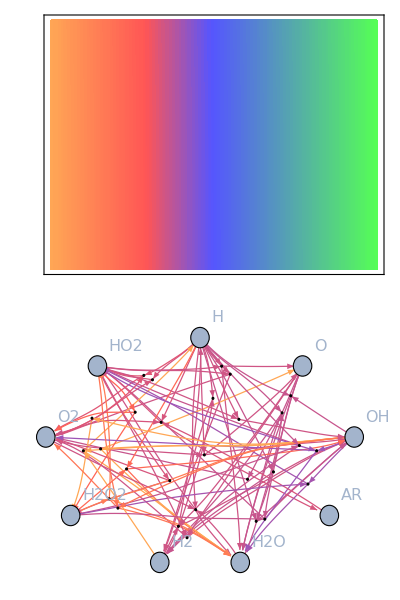

bipartitie2.pdf

```mathematica
p0=Graph[vertices,Flatten[edges],GraphLayout->{"EdgeLayout"->"DividedEdgeBundling"},VertexCoordinates->vcs,VertexLabels->(#->If[IntegerQ[#],"",Style[#,16]]&/@vertices),VertexStyle->(#->If[ValueQ[Element[#,Integers]],{If[MemberQ[bottomreactions,#],{Opacity[0],EdgeForm[None]},{Opacity[1],EdgeForm[Black]}],Black},If[MemberQ[centerspecies,#],{Hue[0.6,0.2,0.8],EdgeForm[Black]},{Opacity[1.0],Blend[spcol/@bottomspecies],EdgeForm[Black]}]]&/@vertices),
VertexSize->(#->If[ValueQ[Element[#,Integers]],{"Scaled",0.005},{"Scaled",0.05}]&/@vertices),EdgeStyle->(#-> If[Abs[eweight[#]]≤0,{Directive[Opacity[0]]},{Directive[Opacity[1.0]],Directive[cf[ecolor[#]]],Thickness[Abs[ethick]],Arrowheads[{{Abs[10*ethick],1.0}}]}]&/@Flatten[edges]),EdgeShapeFunction->(If[Position[vcs,First[#]]≠{},{Arrow[#,{0.0,1.5*vsize[vcs[[FirstPosition[N[vcs],Last[#]][[1]],1]]]}]},{Arrow[#,{0.0,0.01}]}]&),ImageSize->{300,Automatic}];
p=Grid[{{cb1},{p0}}]
Export["bipartitie2.pdf",p]
```

### CME

```mathematica
filebase="data/dimred3/10"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temp=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pres=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
species={"H2","H","O","O2","OH","H2O","HO2","H2O2","AR"};
```

data/dimred3/10

{11106,9,0}

```mathematica
indices=Transpose[{rows,columns}];
reactions=DeleteDuplicates[multiindices[[rows+1]]-multiindices[[columns+1]]];
rindices=Cases[indices,u_/;multiindices[[u[[1]]+1]]-multiindices[[u[[2]]+1]]==#]&/@reactions;
Monitor[AbsoluteTiming[rates2=Table[Total[states[[i,#[[2]]+1]]*A[[#[[2]]+1,#[[1]]+1]]&/@#]&/@rindices,{i,1,Length[states],1}];],i]
rates=-Transpose[rates2][[1;;-1;;2]]+Transpose[rates2][[2;;-1;;2]];
rstois=reactions[[1;;-1;;2]]/.u_/;u<0->0;
pstois=-(reactions[[1;;-1;;2]]/.u_/;u>0->0);
nreactions=Length[rates];
reactants=Table[Extract[species,Position[rstois[[i]],u_/;u>0]],{i,1,nreactions}];
products=Table[Extract[species,Position[pstois[[i]],u_/;u>0]],{i,1,nreactions}];
```

{123.599,Null}

{20,101}

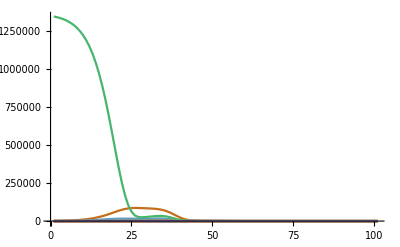

```mathematica
Dimensions[rates]
ListPlot[rates,Joined->True,PlotRange->All]
```

```mathematica
t0=10.^-8;
t1=10^2;
Nt=Length[states];
times=Table[t0*(t1/t0)^(i/(Nt-1)),{i,0,(Nt-1)}];
o2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[4]])/Total[#])&/@multiindices)];h2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[1]])/Total[#])&/@multiindices)];
h2onorm=SparseArray[({#,#}&/@Range[dim])->(((#[[6]])/Total[#])&/@multiindices)];
concentrationnorms=Table[SparseArray[({#,#}&/@Range[dim])->(((#[[i]])/Total[#])&/@multiindices)],{i,1,ns}];
temperaturenorm=SparseArray[({#,#}&/@Range[dim])->(temp)];
pressurenorm=SparseArray[({#,#}&/@Range[dim])->(pres)];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
temperatures=(Total/@(states.temperaturenorm));
pressures=(Total/@(states.pressurenorm));
concentrations=Table[(Total/@(states.concentrationnorms[[i]])),{i,1,ns}];
sptime[text_]:=First@FirstPosition[Accumulate[10^-12+concentrations[[First@FirstPosition[species,text]]]]/Total[10^-12+concentrations[[First@FirstPosition[species,text]]]],u_/;u>0.5]/Nt
sptimemin=Min[sptime/@species];
sptimemax=Max[sptime/@species];
spcol[text_]:=Blend[{Cyan,Orange},(sptime[text]-sptimemin)/(sptimemax-sptimemin)]
```

```mathematica
Tmax=Max[temperatures];
Tmin=Min[temperatures];
Pmax=Max[pressures];
Pmin=Min[pressures];
imagePadding2={{75,75},{1,1}};
imgSize2={500,250};
imagePadding1={{75,75},{50,1}};
imgSize1={500,290};
imgSize3={440*(2.2)/(1.3),440};
tmax=times[[-1]]
reactantnames={"H2","O2","AR"};
productnames={"H2O2","H2O"};
ohintermediates={"H2","H","O","OH","HO2"};
nspecies=Length[species]
cmax=1.1*Max[{concentrations[[First@FirstPosition[species,"H2O"]]],concentrations[[First@FirstPosition[species,"H2"]]][[2]],concentrations[[First@FirstPosition[species,"O2"]]][[2]]}];
cplots={"H2","O2","H2O"};
ccplots=ColorData[97,"ColorList"][[1;;3]];
p1=ListLogPlot[Join[concentrations,(concentrations[[First@FirstPosition[species,#]]])&/@cplots],Joined->True,PlotRange->{10^-12,1},LabelStyle->Directive[16,Black],Axes->False,Frame->True,FrameLabel->{None,DisplayForm[RowBox[{"Mole Fraction,",Subscript[ X,i]}]]},FrameTicks->{{Automatic,{}},Table[{i,""},{i,0,(Nt-1),(Nt-1)/5}]},PlotStyle->Join[ConstantArray[Directive[Thickness[0.005],LightGray],nspecies],Directive[Thickness[0.01],#]&/@ccplots],FrameStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRangeClipping->False,ImagePadding->imagePadding2,ImageSize->imgSize2];
p2=ListPlot[{(temperatures-Tmin)/(Tmax-Tmin)+0.05,(pressures-Pmin)/(Pmax-Pmin)-0.05},Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[4]],Thickness[0.01]],Directive[ColorData[97,"ColorList"][[5]],Thickness[0.01]]},PlotRange->{-0.1,1.1},LabelStyle->Directive[16,Black],Axes->False,Frame->True,FrameLabel->{{Style["Temperature (K)",ColorData[97,"ColorList"][[4]]],Style["Pressure (atm)",ColorData[97,"ColorList"][[5]]]},{"Time (ms)",None}},FrameTicks->{{Table[{(T-Tmin)/(Tmax-Tmin),Style[Round[T],ColorData[97,"ColorList"][[4]]]},{T,Tmin,Tmax,(Tmax-Tmin)/3}],Table[{(P-Pmin)/(Pmax-Pmin),Style[PaddedForm[P,{3,2}],ColorData[97,"ColorList"][[5]]]},{P,Pmin,Pmax,(Pmax-Pmin)/3}]},{Table[{i,times[[i]]/10^-3},{i,1,Nt,Round[Length[times]/5]}],{}}},FrameStyle->Directive[Black,AbsoluteThickness[1.5]],ImagePadding->imagePadding1,ImageSize->imgSize1];
```

100.

9

InterpolatingFunction::dmval: Input value {1/101} lies outside the range of data in the interpolating function. Extrapolation will be used.

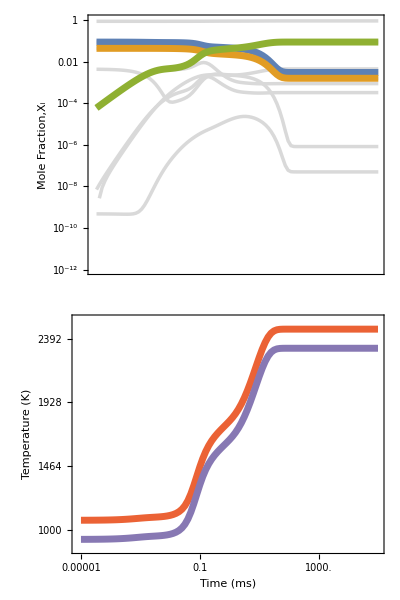
-Graphics- | -Graphics-

h2o2CMEbipartite.pdf

```mathematica
maxt=60;
cb=MatrixPlot[Table[Blend[{Red,Blue},N[i/100]],{j,1,2},{i,0,maxt}],AspectRatio->1/10,PlotRange->{{1,2},{0,100}},PlotRangePadding->None,FrameTicks->{{None,None},{None,Table[{i,Superscript[10,3+Round[Log[times[[i]]]/Log[10]]]},{i,1,101,20}]}},FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->250,LabelStyle->Directive[16,Black],FrameLabel->{{None,DisplayForm[RowBox[{t," (ms)"}]]},{None,None}}];

r1=1.5;
r2=1;
colors={Lighter[Red],Lighter[Blue]};
weights=Mean/@rates;
weights2=First@FirstPosition[Abs[#],Max[Abs[#]]]&/@rates/Nt;
wscale=Max[Abs[weights]];
ethrs=10^-1;
ethick=0.003;
shown=Flatten[Position[weights,u_/;Abs[u]>ethrs]];
edges=Table[If[weights[[i]]>0,Join[Table[reactants[[i,j]]->i,{j,1,Length[reactants[[i]]]}],Table[i->products[[i,j]],{j,1,Length[products[[i]]]}]],Join[Table[i->reactants[[i,j]],{j,1,Length[reactants[[i]]]}],Table[products[[i,j]]->i,{j,1,Length[products[[i]]]}]]],{i,1,nreactions}];
vertices=Union[species,DeleteDuplicates[Flatten[edges][[All,1]],Flatten[edges][[All,2]]]];
center=DeleteDuplicates[Join[Flatten[edges[[shown,All,1]]],Flatten[edges[[shown,All,2]]]]];
(*centerspecies=SortBy[Complement[DeleteDuplicates[DeleteDuplicates[Join[Flatten[edges[[shown,All,1]]],Flatten[edges[[shown,All,2]]]]]],Range[nreactions]],spcol[#]&];*)
centerspecies=SortBy[species,spcol[#]&];
centerreactions=Complement[center,centerspecies];
bottomspecies=SortBy[Complement[species,centerspecies],spcol[#]&];
bottomreactions=Complement[Range[nreactions],centerreactions];
rvcs=GraphEmbedding[PathGraph[Flatten[Position[weights,u_/;Abs[u]>ethrs]],GraphLayout->"SpiralEmbedding"]];
rvcs2=GraphEmbedding[PathGraph[Flatten[Position[weights,u_/;Abs[u]<=ethrs]],GraphLayout->"SpiralEmbedding"]];
{xmax,xmin,ymax,ymin}={Max[rvcs[[All,1]]],Min[rvcs[[All,1]]],Max[rvcs[[All,2]]],Min[rvcs[[All,2]]]};
{xmax2,xmin2,ymax2,ymin2}={Max[rvcs2[[All,1]]],Min[rvcs2[[All,1]]],Max[rvcs2[[All,2]]],Min[rvcs2[[All,2]]]};
transform[p_]:=1.5*{r1,r2}*{(p[[2]]-ymin)/(ymax-ymin)-1/2,(p[[1]]-xmin)/(xmax-xmin)-1/2};
transform2[p_]:=1.5*{r1,r2}*{(p[[2]]-ymin2)/(ymax2-ymin2)-1/2,(p[[1]]-xmin2)/(xmax2-xmin2)-1/2};
trange=Quantile[Extract[weights2,Position[weights,u_/;Abs[u]>ethrs]],{0.25,0.75}];
trange={1/Nt,maxt/Nt};
eweight[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights[[edge[[1]]]],weights[[edge[[2]]]]];
ecolor[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights2[[edge[[1]]]],weights2[[edge[[2]]]]];
vsize[text_]:=0.005+0.08*(Log[Max[Mean[concentrations[[First@FirstPosition[species,text]]]],10^-8]]/Log[10]+8)/8;
sizes={1.0,0.1,0.01,0.001,0.0001};
wsizes=Table[z/.First@Solve[(Log[Abs[z/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])==i*1.0/5,z],{i,5,1,-1}];
vcs=Join[Table[centerspecies[[i]]->{r1*Cos[3*Pi/2-Pi/12-(2*Pi-2*Pi/12)*(i-1)/(Length[centerspecies]-1)],r2*Sin[3*Pi/2-Pi/12-(2*Pi-2*Pi/12)*(i-1)/(Length[centerspecies]-1)]},{i,1,Length[centerspecies]}],
Table[bottomspecies[[i]]->{0,-r2},{i,1,Length[bottomspecies]}],Table[i->If[MemberQ[centerreactions,i],transform[rvcs[[First@FirstPosition[SortBy[Flatten[Position[weights,u_/;Abs[u]>ethrs]],weights2[[#]]&],i]]]],transform2[rvcs2[[First@FirstPosition[SortBy[Flatten[Position[weights,u_/;Abs[u]<=ethrs]],weights2[[#]]&],i]]]]],{i,nreactions}]];
p0=Graph[vertices,Flatten[edges],GraphLayout->{"EdgeLayout"->"DividedEdgeBundling"},VertexCoordinates->vcs,VertexLabels->(#->If[IntegerQ[#],"",Style[#,16]]&/@vertices),VertexStyle->(#->If[ValueQ[Element[#,Integers]],{If[MemberQ[bottomreactions,#],{Opacity[0],EdgeForm[None]},{Opacity[1],EdgeForm[Black]}],Black},If[MemberQ[centerspecies,#],{spcol[#],EdgeForm[Black]},{Opacity[1.0],Blend[spcol/@bottomspecies],EdgeForm[Black]}]]&/@vertices),
VertexSize->(#->If[ValueQ[Element[#,Integers]],{"Scaled",0.005},If[MemberQ[centerspecies,#],{"Scaled",0.7*vsize[#]},{"Scaled",0.7*Mean[vsize/@bottomspecies]}]]&/@vertices),EdgeStyle->(#-> If[Abs[eweight[#]]<=ethrs,{Directive[Opacity[0]]},{Directive[Opacity[1.0]],Directive[Blend[colors,(ecolor[#]-trange[[1]])/(trange[[2]]-trange[[1]])]],Thickness[Abs[ethick*(Log[Abs[eweight[#]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])]],Arrowheads[{{Abs[10*ethick*(Log[Abs[eweight[#]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])],1.0}}]}]&/@Flatten[edges]),EdgeShapeFunction->(If[Position[vcs,First[#]]≠{},{Arrow[#,{0.0,1.5*vsize[vcs[[FirstPosition[N[vcs],Last[#]][[1]],1]]]}]},{Arrow[#,{0.0,0.01}]}]&),ImageSize->{1000,500}];
p=Show[p0,Prolog->{Inset[Grid[{{
MatrixPlot[Table[Directive[Opacity[1.0],Blend[colors,(y-trange[[1]])/(trange[[2]]-trange[[1]])]],{y,trange[[1]],trange[[2]],(trange[[2]]-trange[[1]])/100},{x,1,100}],AspectRatio->10,ImageSize->{125,175},ImagePadding->{{5,90},{10,5}},FrameTicks->{{None,Table[{i,PaddedForm[tint[(trange[[1]]+(i-1)*(trange[[2]]-trange[[1]])/100)]/10^-3,{3,2}]},{i,1,101,20}]},{None,None}},PlotRangePadding->None,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{None,"Reaction Time (ms)"}},RotateLabel->True,DataReversed->{True,True}]},{Graphics[{{Table[{EdgeForm[Black],White,Disk[{-1.0,-1.25*i},12*(0.005+0.08*(Log[sizes[[i]]]/Log[10]+8)/8)],Black,Text[Style[With[{n=i},HoldForm[10^(-n)]],16],{-2.8,-1.25*i}]},{i,1,Length[sizes]}]},Rotate[Text[Style["Mole Fraction",16],{-4.0,-4}],Pi/2]},PlotRange->{{-5,0.1},{-8,0}},ImageSize->{125,175}]}}],{2.6,0.0}]},ImageSize->{1000,500},PlotRange->{{-2,3.3},{-1.3,1.25}},PlotRangePadding->None];
p3=Grid[{{Grid[{{Show[p1,Epilog->{Inset[Style["(a)",18],ImageScaled[{0,1}],Scaled[{0,1}]]},PlotRangeClipping->False]},{Show[p2,Epilog->{Inset[Style["(b)",18],ImageScaled[{0,1}],Scaled[{0,1}]]},PlotRangeClipping->False]}},Alignment->Left,Spacings->0],Show[p,Epilog->{Inset[Style["(c)",18],Scaled[{0,1}],Scaled[{0,1}]]}]}},Spacings->0]
Export["h2o2CMEbipartite.pdf",p3]
```

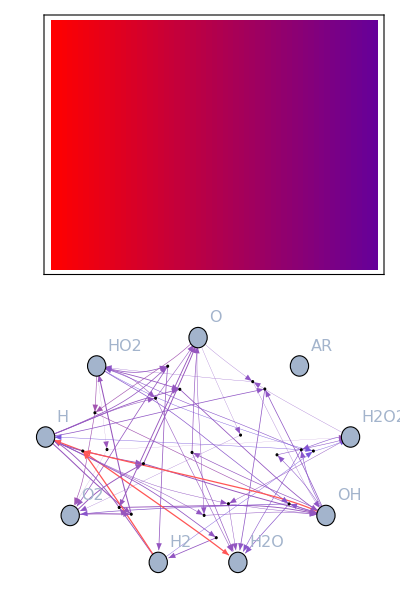

bipartitie.pdf

```mathematica
cb=MatrixPlot[Table[Blend[{Red,Blue},N[i/100]],{j,1,2},{i,0,maxt}],AspectRatio->1/10,PlotRange->{{1,2},{0,100}},PlotRangePadding->None,FrameTicks->{{None,None},{None,Table[{i,Superscript[10,3+Round[Log[times[[i]]]/Log[10]]]},{i,1,101,20}]}},FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->200,LabelStyle->Directive[16,Black],FrameLabel->{{None,DisplayForm[RowBox[{t," (ms)"}]]},{None,None}}];

p0=Graph[vertices,Flatten[edges],GraphLayout->{"EdgeLayout"->"DividedEdgeBundling"},VertexCoordinates->vcs,VertexLabels->(#->If[IntegerQ[#],"",Style[#,16]]&/@vertices),VertexStyle->(#->If[ValueQ[Element[#,Integers]],{If[MemberQ[bottomreactions,#],{Opacity[0],EdgeForm[None]},{Opacity[1],EdgeForm[Black]}],Black},If[MemberQ[centerspecies,#],{Hue[0.6,0.2,0.8],EdgeForm[Black]},{Opacity[1.0],Blend[spcol/@bottomspecies],EdgeForm[Black]}]]&/@vertices),
VertexSize->(#->If[ValueQ[Element[#,Integers]],{"Scaled",0.005},{"Scaled",0.05}]&/@vertices),EdgeStyle->(#-> If[Abs[eweight[#]]<=ethrs,{Directive[Opacity[0]]},{Directive[Opacity[1.0]],Directive[Blend[colors,(ecolor[#]-trange[[1]])/(trange[[2]]-trange[[1]])]],Thickness[Abs[ethick*(Log[Abs[eweight[#]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])]],Arrowheads[{{Abs[10*ethick*(Log[Abs[eweight[#]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])],1.0}}]}]&/@Flatten[edges]),EdgeShapeFunction->(If[Position[vcs,First[#]]≠{},{Arrow[#,{0.0,1.5*vsize[vcs[[FirstPosition[N[vcs],Last[#]][[1]],1]]]}]},{Arrow[#,{0.0,0.01}]}]&),ImageSize->{300,Automatic}];
p=Grid[{{cb},{p0}}]
Export["bipartitie.pdf",p]
```

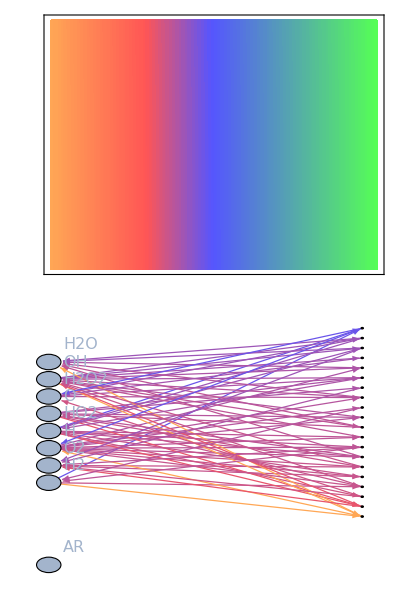

bipartitie1.pdf

```mathematica
weights2=First@FirstPosition[Abs[#],Max[Abs[#]]]&/@rates;
ecolor[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights2[[edge[[1]]]],weights2[[edge[[2]]]]]
p0=Graph[Flatten[{SortBy[species,sptime],SortBy[Range[Length[edges]],ecolor[edges[[#,1]]]&]}],Flatten[edges],GraphLayout->"BipartiteEmbedding",VertexLabels->(#->If[IntegerQ[#],"",Style[#,16]]&/@vertices),VertexStyle->(#->If[ValueQ[Element[#,Integers]],{If[MemberQ[bottomreactions,#],{Opacity[0],EdgeForm[None]},{Opacity[1],EdgeForm[Black]}],Black},If[MemberQ[centerspecies,#],{Hue[0.6,0.2,0.8],EdgeForm[Black]},{Opacity[1.0],Hue[0.6,0.2,0.8],EdgeForm[Black]}]]&/@vertices),
VertexSize->(#->If[ValueQ[Element[#,Integers]],{"Scaled",0.005},If[MemberQ[centerspecies,#],{"Scaled",0.05},{"Scaled",0.05}]]&/@vertices),EdgeStyle->(#-> If[Abs[eweight[#]]≤0,{Directive[Opacity[0]]},{Directive[Opacity[1.0]],Directive[cf[ecolor[#]]],Thickness[ethick],Arrowheads[{{Abs[10*ethick],1.0}}]}]&/@Flatten[edges]),EdgeShapeFunction->((If[#[[1,1]]>#[[2,1]],{Arrow[#,{0.0,0.075}]},{Arrow[#,{0.0,0.015}]}])&),ImageSize->{300,Automatic}];
p=Grid[{{cb1},{p0}}]
Export["bipartitie1.pdf",p]
```

{O→O2,H→OH,O→OH,H2→H,H2→OH,O→H,O→OH,O→O2,HO2→O2,O→OH,HO2→OH,O→OH,H2O2→OH,O→HO2,H2O2→HO2,H→HO2,O2→HO2,H→O,H→OH,O2→O,O2→OH,H→H2,H→H2O,OH→H2O,H→O,HO2→O,H→H2O,HO2→H2O,H→H2,HO2→H2,H→O2,HO2→O2,H→OH,HO2→OH,H2→H,H2→H2O2,HO2→H,HO2→H2O2,H→OH,H2O2→OH,H→H2O,H2O2→H2O,H2→H,H2→H2O,OH→H,OH→H2O,OH→H2O2,OH→O,OH→H2O,OH→O2,HO2→O2,OH→H2O,HO2→H2O,OH→H2O,H2O2→H2O,OH→HO2,H2O2→HO2,HO2→O2,HO2→H2O2}

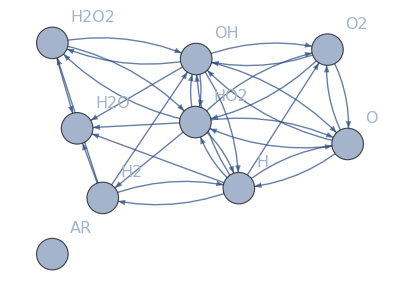

species.pdf

```mathematica
edges2=Flatten[Table[If[Abs[weights[[i]]]>ethrs,If[weights[[i]]>0,Table[reactants[[i,j]]->products[[i,k]],{j,1,Length[reactants[[i]]]},{k,1,Length[products[[i]]]}],Table[products[[i,j]]->reactants[[i,k]],{k,1,Length[reactants[[i]]]},{j,1,Length[products[[i]]]}]],{}],{i,1,nreactions}]]

g=Graph[species,DeleteDuplicates[edges2],VertexLabels->(#->Style[#,16]&/@species),VertexSize->0.5]
Export["species.pdf",g]
```